```mathematica
FullSimplify[DSolve[a*(a^4-2*a^2*kappa+1)Phi''[a]+2*(3 a^4-5 a^2 kappa+2)Phi'[a]+a(4 a^2+k^2-8kappa)Phi[a]==0,Phi[a],a]]
```

{{Phi[a]→C[1] HeunG[-1+2 kappa (kappa+√(-1+kappa^2)),(k^2-8 kappa)/(4 (-kappa+√(-1+kappa^2))),1/2,2,5/2,1/2,a^2 (kappa+√(-1+kappa^2))]+((kappa-√(-1+kappa^2)) C[2] HeunG[-1+2 kappa (kappa+√(-1+kappa^2)),(k^2-2 kappa)/(4 (-kappa+√(-1+kappa^2))),-1,1/2,-1/2,1/2,a^2 (kappa+√(-1+kappa^2))])/(a^2 √(a^2 (kappa+√(-1+kappa^2))))}}

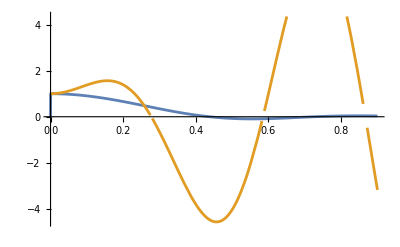

```mathematica
Plot[{HeunG[-1+2 kappa (kappa+√(-1+kappa^2)),(k^2-8 kappa)/(4 (-kappa+√(-1+kappa^2))),1/2,2,5/2,1/2,a^2 (kappa+√(-1+kappa^2))]/.kappa->.5/.k->10,HeunG[-1+2 kappa (kappa+√(-1+kappa^2)),(k^2-2 kappa)/(4 (-kappa+√(-1+kappa^2))),-1,1/2,-1/2,1/2,a^2 (kappa+√(-1+kappa^2))]/.kappa->.5/.k->10},{a,0,0.9}]
```

```mathematica
(* Pick the solution, which amplitude drop when "a" increase. *)
soln1=FullSimplify[DSolve[{a*(a^4-2*a^2*kappa+1)Phi''[a]+2*(3 a^4-5 a^2 kappa+2)Phi'[a]+a(4 a^2+k^2-8kappa)Phi[a]==0,Phi[0]==1,Phi'[0]==0},Phi[a],a]][[1,1,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

HeunG[-1+2 kappa (kappa+√(-1+kappa^2)),(k^2-8 kappa)/(4 (-kappa+√(-1+kappa^2))),1/2,2,5/2,1/2,a^2 (kappa+√(-1+kappa^2))]

(-1)^((-1+kappa^2+√(1-kappa^2)-ⅈ kappa √(1-kappa^2))/(4 (-1+kappa^2))) ⅇ^(-1/4 ArcTanh[(2 a^2 kappa)/(1+a^4)]-((ⅈ+kappa) (ArcTanh[(a^2-kappa)/(√(-1+kappa^2))]+ArcTanh[kappa/(√(-1+kappa^2))]))/(2 √(-1+kappa^2))) (1+a^8+a^4 (2-4 kappa^2))^(1/8) (-1+a^2 (kappa+ⅈ √(1-kappa^2)))^(-(-1+kappa^2+√(1-kappa^2)-ⅈ kappa √(1-kappa^2))/(4 (-1+kappa^2))) (1+ⅈ a^2 (ⅈ kappa+√(1-kappa^2)))^((-1+kappa^2+√(1-kappa^2)-ⅈ kappa √(1-kappa^2))/(4 (-1+kappa^2))) HeunG[-1/((ⅈ kappa+√(1-kappa^2))^2),1/4 (-ⅈ kappa+√(1-kappa^2)) (-ⅈ k^2+13 ⅈ kappa+5 √(1-kappa^2)),1,5/2,5/2,1/2,a^2 (kappa+ⅈ √(1-kappa^2))]

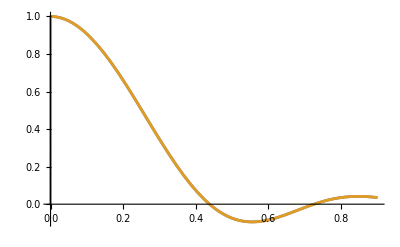

```mathematica
alpha=ⅈ*kappa+√(1-kappa^2);
gamma=(alpha*(alpha-1))/(2*alpha^2+2);
Phi=FullSimplify[(1+2*(1-2*kappa^2)*a^4+a^8)^(1/8)((ⅈ*a^2)/alpha-1)^-gamma(ⅈ*alpha*a^2+1)^gamma*Exp[-1/4*ArcTanh[(2*a^2*kappa)/(1+a^4)]+(ⅈ+kappa)/(2*√(kappa^2-1))ArcTanh[(-a^2+kappa)/(√(kappa^2-1))]]HeunG[-1/alpha^2,(-(ⅈ k^2-8 ⅈ kappa-5*alpha))/(4*alpha),1,5/2,5/2,1/2,(ⅈ*a^2)/alpha]];
Phi0=Phi/.a->0;
soln2=FullSimplify[Phi/Phi0]
Plot[{soln1/.kappa->.5/.k->10,soln2/.kappa->.5/.k->10},{a,0.,0.9}]
```

#### Integration form

0

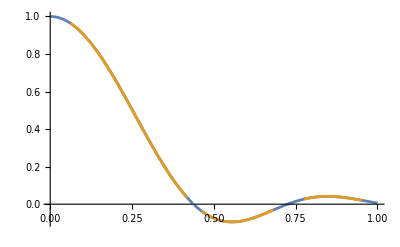

```mathematica
(*Integration form*)
Clear[f,psi,ϕ]
f[kc_,a_]:=3*Sqrt[a^4+(K^2-2*kc)*a^2+1]/K/Sqrt[(K^2-2*kc)^2-4]/a^3;
psi[kc_,a_]:=Sqrt[kc-Sqrt[kc^2-1]]*(EllipticPi[-1/2*(kc-Sqrt[kc^2-1])*((K^2-2*kc)-Sqrt[(K^2-2*kc)^2-4]),ArcSin[a/Sqrt[kc-Sqrt[kc^2-1]]],(Sqrt[kc^2-1]-kc)^2]-EllipticPi[-1/2*(kc-Sqrt[kc^2-1])*((K^2-2*kc)+Sqrt[(K^2-2*kc)^2-4]),ArcSin[a/Sqrt[kc-Sqrt[kc^2-1]]],(Sqrt[kc^2-1]-kc)^2]);
 ϕ[kc_,a_]:=f[kc,a]*Sin[K*psi[kc,a]];
(a(1+a^4)-2a^3 kc)D[ϕ[kc,a],{a,2}]+(2(3a^4+2)-10a^2 kc)D[ϕ[kc,a],{a,1}]+a(4a^2+K^2-8 kc)ϕ[kc,a]//FullSimplify
Plot[{soln1/.kappa->0.5/.k->10, ϕ[0.5,a]/.K->10},{a,0.001,1}]
```